```mathematica
Import["E:\\MyWorkShop\\midi\\notebooks\\midilib.nb"];
```

```mathematica
Clear[musictemplate]
```

```mathematica
deltaseq[x_List]:=Differences;
```

```mathematica
deltaseq[1]
```

deltaseq[1]

```mathematica
Clear[deltaseq]
```

```mathematica
Manipulate[
ListPlot[
Accumulate[
{x[[2]]}~Join~
Accumulate[
{x[[1]]}~Join~{1,2,-5,4,-3,6,1}]
],
PlotRange->Full,Joined->True,Mesh->All
],
Control[{x,{-4,-4},{4,4},0.1}]
]
```

```mathematica
Manipulate[
Sound[SoundNote[Round[#],0.2]&/@Accumulate[
{x[[2]]}~Join~
Accumulate[
{x[[1]]}~Join~{-3,4,-5,5,-4,4,-2}]
]
]
,
Control[{x,{-4,-4},{4,4},0.1}]
]
```

```mathematica
Manipulate[
data=Fold[
Accumulate[Insert[#1,#2,RandomInteger[{1,Length[#1]}]]]&,{-.01,-.05,.1,-2,-0.3,-.1},x[[1;;length]]
];ListPlot[
data,
PlotRange->Full,Joined->True,Mesh->All
],
{{length,5},1,10,1},
{{x,Table[0,{i,1,30}]},ControlType->None},
Dynamic[Row@Outer[Slider[Dynamic[x[[#1]]],{-0.5,0.5}]&,Range[length]]]
]
```

```mathematica
Clear[li,l2,f1]
li={Cos[x]-2Sin[x],8Cos[10x]-9Sin[10x],-Cos[3x]+0.6Sin[3x],2Cos[4x]}
l2=1/3 Plus@@li
f1[t_]:=-0.4
DiscretePlot[l2,{x,-4Pi,4Pi,1/40 Pi}]
```

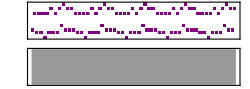

```mathematica
Sound@musictemplate[List/@(CMajor/@Round@Array[10+l2/.x->(#*1/10 Pi)&,100]),0.2]
```

```mathematica
musictemplate[{{1},{3},{5}},0.2]
```

{SoundNote[1,{0.2,0.44},Piano],SoundNote[3,{0.4,0.64},Piano],SoundNote[5,{0.6,0.84},Piano]}

```mathematica
Export["E:\\MyWorkShop\\midi\\demo.mid",Sound@musictemplate[
List/@(CMajor/@Round@Array[l2/.x->(#*1/10 Pi)&,100]),0.15]]
```

E:\MyWorkShop\midi\demo.mid

```mathematica
EmitSound[%481]
```

EmitSound[%481]

```mathematica
N@Array[Plus@@li/.x->(#*Pi)&,50]
```

{10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.}

```mathematica
randomsinusoid[len_]:=Table[RandomComplex[{-3-3I,3+3I}],{i,1,len}]
```

```mathematica
synthetize[ingre_]:=Plus@@MapIndexed[#1*E^(2Pi ⅈ (#2[[1]]-1)x)+Conjugate[#1]*E^(2Pi ⅈ(1-#2[[1]])x)&,ingre]
```

```mathematica
randomsinusoid[8]
```

{-2.49012+0.575478 ⅈ,-0.324604+2.38509 ⅈ,-0.777139+2.89526 ⅈ,2.1392-1.26265 ⅈ,0.0735779+1.1113 ⅈ,-1.87081+2.96822 ⅈ,-2.04614-2.51585 ⅈ,2.43442-0.433813 ⅈ}

```mathematica
synthetize[randomsinusoid[8]]
```

(3.19648+0. ⅈ)+(2.5001-0.286782 ⅈ) ⅇ^(-2 ⅈ π x)+(2.5001+0.286782 ⅈ) ⅇ^(2 ⅈ π x)+(0.459633+0.176403 ⅈ) ⅇ^(-4 ⅈ π x)+(0.459633-0.176403 ⅈ) ⅇ^(4 ⅈ π x)-(0.0167887+2.75794 ⅈ) ⅇ^(-6 ⅈ π x)-(0.0167887-2.75794 ⅈ) ⅇ^(6 ⅈ π x)+(2.65711-2.2142 ⅈ) ⅇ^(-8 ⅈ π x)+(2.65711+2.2142 ⅈ) ⅇ^(8 ⅈ π x)-(2.05273+0.453504 ⅈ) ⅇ^(-10 ⅈ π x)-(2.05273-0.453504 ⅈ) ⅇ^(10 ⅈ π x)-(0.685545+0.878823 ⅈ) ⅇ^(-12 ⅈ π x)-(0.685545-0.878823 ⅈ) ⅇ^(12 ⅈ π x)-(0.56413-2.83456 ⅈ) ⅇ^(-14 ⅈ π x)-(0.56413+2.83456 ⅈ) ⅇ^(14 ⅈ π x)

-4+1/2 ⅇ^(-2 ⅈ π x)+1/2 ⅇ^(2 ⅈ π x)-2/9 ⅇ^(-4 ⅈ π x)-2/9 ⅇ^(4 ⅈ π x)+1/8 ⅇ^(-6 ⅈ π x)+1/8 ⅇ^(6 ⅈ π x)-2/25 ⅇ^(-8 ⅈ π x)-2/25 ⅇ^(8 ⅈ π x)

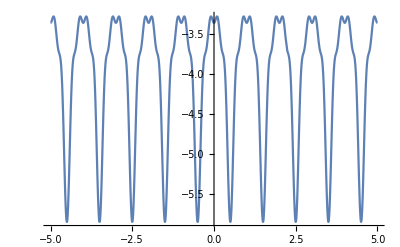

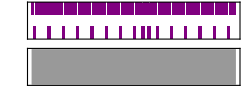

```mathematica
tone=synthetize[{-2,1/2,-2/9,1/8,-2/25}]
Plot[tone,{x,-5,5}]
Sound@musictemplate[
List/@(CMajor/@Round@(1/10*Array[tone/.x->(#*2/1 Pi)&,100])),0.15]
```

```mathematica
gen[l_]:=
Module[
{tone=synthetize[l]},
Column@{Plot[tone,{x,-1,1}],sound=Sound@musictemplate[
List/@(CMajor/@Round@(1/10*Array[tone/.x->(#*3/20Pi)&,200])),0.3,"Piano"]}
]
```

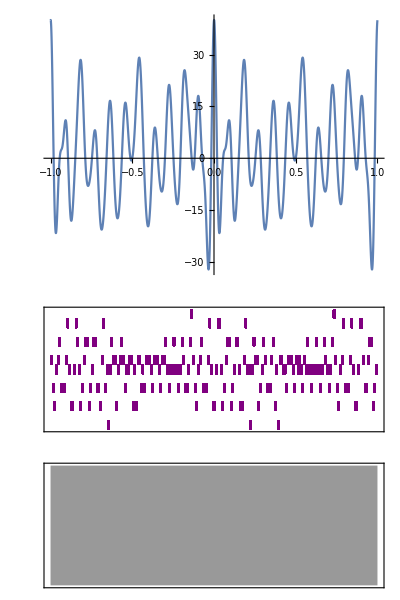

```mathematica
gen[{1,1I,0,-3,1,0,2-3I,0,0,0,0,8,1,1,1,1,1,1,1,1,1,1,1}]
```

```mathematica
Export["E:\\MyWorkShop\\midi\\demo4.mid",sound]
```

E:\MyWorkShop\midi\demo4.mid

```mathematica
manitone[tone_]:=musictemplate[
List/@(CMajor/@Round@(1/10*Array[tone/.x->(#*1/20)&,10,-5])),0.3,"Piano"]
toneplay[tone_]:=Sound[]
longgen[l_]:=
Module[
{tone=synthetize[l]},
Column@{Plot[tone,{x,0,1/5}],sound=Sound@musictemplate[
List/@(CMajor/@Round@(1/10*Array[tone/.x->(#*1/50)&,10,0])),0.3,"Piano"]}
]
```

```mathematica
Manipulate[longgen[{5, 20I,3i[[1]]+2i[[2]] I,0,0.1,0,0,-0.2I,0,0,0,0,0,0,0,0,0,0,-2,2I,3-2I,0,0,0,4-j}],{i,{-10,-10},{10,10}},{j,-20,20}]
```

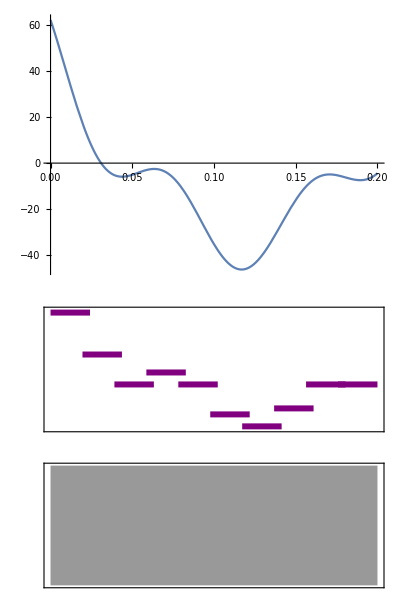

```mathematica
longgen[{0,0,0,0,20,0,8-I,9I,0,0,3,10I}]
```

```mathematica
long[tone_,nu_]:=
List/@(CMajor/@Round@(1/10*Array[synthetize[tone]/.x->(nu*1/5+#*1/50)&,10,0]))
```

```mathematica
Clear[mytone,ftone];
mytone={0,0,0,0,0,0,-I,4I,0,0,0,5I};
mymusic=long[mytone,0];
ftone=mytone;
ftone[[1]]=ftone[[1]]-5;
music1=long[ftone,0];
Do[
Modifier=RandomComplex[{-1-1I,1+1I},Length[mytone]];
mytone=mytone+Modifier;
mymusic=mymusic~Join~long[mytone,i*1];
music1=music1~Join~long[ftone,i*1];
,{i,1,20}]
```

```mathematica
Column@{mytone}
```

{10.0015-2.08178 ⅈ,-4.90085+2.10142 ⅈ,0.536549-0.655445 ⅈ,0.0841304-3.34214 ⅈ,0.902162+4.37482 ⅈ,1.85177+5.99931 ⅈ,0.719863+1.67582 ⅈ,3.04975-0.0113548 ⅈ,2.90536-0.844651 ⅈ,6.63382-0.690041 ⅈ,4.26106+0.809918 ⅈ,0.714389+1.02101 ⅈ,-1.72149+5.47014 ⅈ,1.89154-2.66254 ⅈ,-0.515178-3.05572 ⅈ}

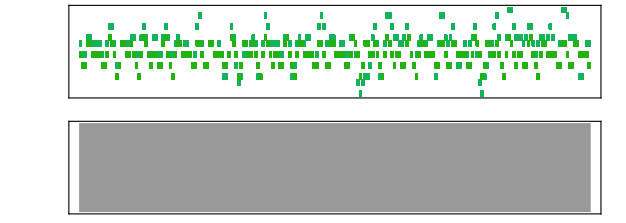

```mathematica
Sound[musictemplate[mymusic,0.2,"Guitar"]~Join~musictemplate[music1,0.2,"ElectricBass"]]
```

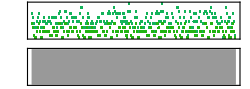

```mathematica
Sound[musictemplate[mymusic,0.2,"Guitar"]~Join~musictemplate[music1,0.2,"ElectricBass"]]
```

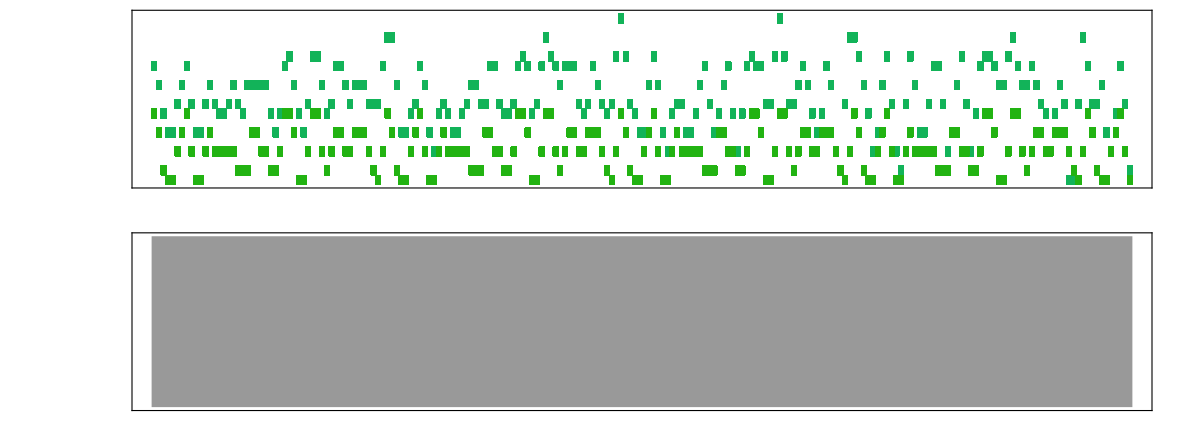

```mathematica
demo5吉他和贝斯=Sound[musictemplate[mymusic,0.2,"Guitar"]~Join~musictemplate[music1,0.2,"ElectricBass"]]
```

```mathematica
Export["E:\\MyWorkShop\\midi\\demo5吉他和贝斯.mid",demo5吉他和贝斯]
```

E:\MyWorkShop\midi\demo5吉他和贝斯.mid

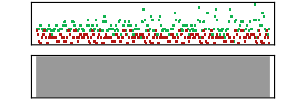

```mathematica
demo5双乐器=Sound[musictemplate[mymusic,0.2,"Viola"]~Join~musictemplate[music1,0.2,"Trumpet"]]
```

```mathematica
long[{0,1,1},1]
```

long[{0,1,1},1]